```mathematica
(* Theoretical Result: j=3/2, l=1 basis states for the Subscript[Γ, 8] representation of the Subscript[T, d] double group *)
ψ32[x_,y_,z_]:={x+I y,0}/Sqrt[2];
ψ12[x_,y_,z_]:={-Sqrt[2/3]z,(x+I y)/Sqrt[6]};
ψm12[x_,y_,z_]:={-(x-I y)/Sqrt[6],-z Sqrt[2/3]};
ψm32[x_,y_,z_]:={0,-(x-I y)/Sqrt[2]};
```

## Generate test data

```mathematica
(*Number of points for which the wavefunction is sampled along each dimension, x, y and z. *)
npts=21;
(*Location of data file*)
pathToFile=NotebookDirectory[]<>"../exampledata_npts21.OUT";
```

```mathematica
psi=Import[pathToFile,"Table"];
```

## Projections

```mathematica
coords=Table[Round[{psi[[ii,1]],psi[[ii,2]],psi[[ii,3]]},10^-6],{ii,1,Length[psi]}];
```

```mathematica
h=Length[Ρ[1][[1]]]; (* dimensonality of the representaton *)
L; (* number of elements in the group - defined in Td_realspace_rot.nb *)

UP=Table[{coords[[ii]],psi[[ii,4]]+I*psi[[ii,5]]},{ii,1,Length[psi]}];
DOWN=Table[{coords[[ii]],psi[[ii,6]]+I*psi[[ii,7]]},{ii,1,Length[psi]}];


state[r_]:={Interpolation[UP][r[[1]],r[[2]],r[[3]]],Interpolation[DOWN][r[[1]],r[[2]],r[[3]]]}

rstate[n_,r_]:=rs[n].state[Rm[n].{r[[1]],r[[2]],r[[3]]}]
Proj[ii_,jj_,r_]:=h/L*Sum[Ρ[n][[ii,jj]]**rstate[n,r],{n,1,L}]
```

## -3/2 ->-3/2

Plotting the projection of the input state onto ψm32 state (which corresponds to the heavy hole down state). We plot here real and imaginary parts of the spin-up and spin-down components. For each plot, we fix coordinates and vary the third. As can be seen from the first cell, the basis states for the Γ_8 representation of the T_d double group can be written in terms of x,y, and z. Therefore, we expect the plots to linear in the components that contribute to the state. Specifically, we expect non negligible values only for spin down plots. Furthermore, only the real part for of the function as x is varied and the imaginary part of the function while y is varied should be no-zero.

### spin up

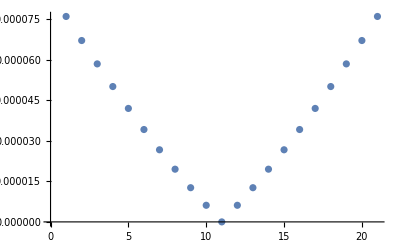
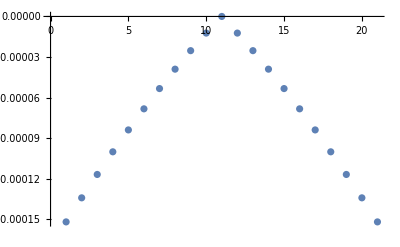
{-Graphics-,-Graphics-,-Graphics-}

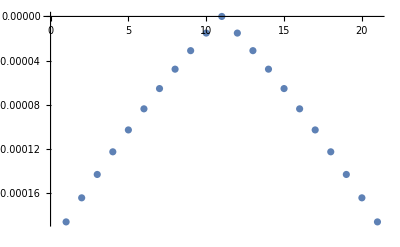
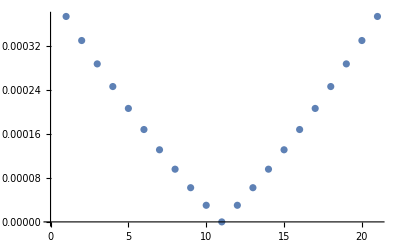
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{ListPlot[ParallelTable[Re[Proj[1,1,{x,0,0}][[1]]],{x,-0.1,0.1,0.01}]],ListPlot[ParallelTable[Re[Proj[1,1,{0,x,0}][[1]]],{x,-0.1,0.1,0.01}]], ListPlot[ParallelTable[Re[Proj[1,1,{0,0,x}][[1]]],{x,-0.1,0.1,0.01}]]}

{ListPlot[ParallelTable[Im[Proj[1,1,{x,0,0}][[1]]],{x,-0.1,0.1,0.01}]],ListPlot[ParallelTable[Im[Proj[1,1,{0,x,0}][[1]]],{x,-0.1,0.1,0.01}]], ListPlot[ParallelTable[Im[Proj[1,1,{0,0,x}][[1]]],{x,-0.1,0.1,0.01}]]}
```

These plots can be approximated by 0 since they are an order of magnitude smaller than the plots for the spin down part of the wavefunciton.

### spin down

```mathematica
(*The projection operators are linear and can therefore output a basis state scaled by some constant. Here we attempt to remove the phase so that the state will take the form of the states from the expression ψm32*)
ϕ=Exp[-I*Arg[Proj[1,1,{0.01,0,0}][[2]]]]
```

0.926122-0.377225 ⅈ

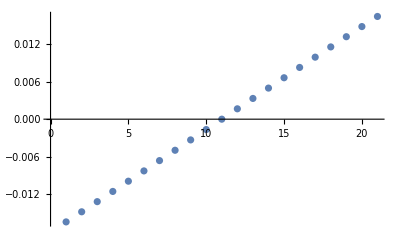
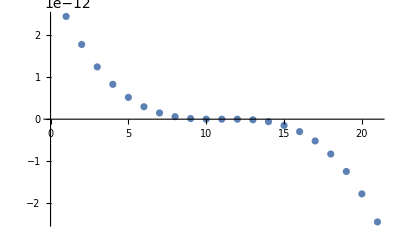
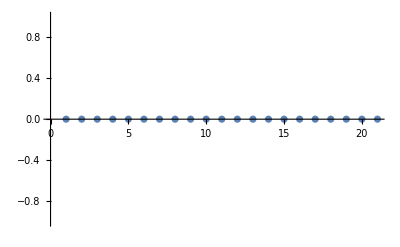

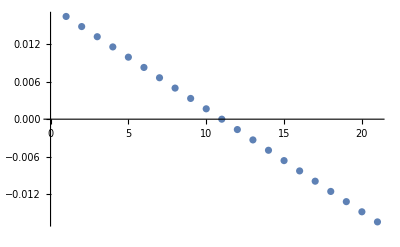
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{ListPlot[ParallelTable[Re[ϕ*Proj[1,1,{x,0,0}][[2]]],{x,-0.1,0.1,0.01}]],ListPlot[ParallelTable[Re[ϕ*Proj[1,1,{0,x,0}][[2]]],{x,-0.1,0.1,0.01}]], ListPlot[ParallelTable[Re[ϕ*Proj[1,1,{0,0,x}][[2]]],{x,-0.1,0.1,0.01}]]}
{ListPlot[ParallelTable[Im[ϕ*Proj[1,1,{x,0,0}][[2]]],{x,-0.1,0.1,0.01}]],ListPlot[ParallelTable[Im[ϕ*Proj[1,1,{0,x,0}][[2]]],{x,-0.1,0.1,0.01}]], ListPlot[ParallelTable[Im[ϕ*Proj[1,1,{0,0,x}][[2]]],{x,-0.1,0.1,0.01}]]}
```

As expected, only two plots have non-negligible values. Comparing these two plots to the theoretical results from the first cell, we see that have agreement.